```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
l=BinaryReadList["test1-carry-sigma=1_0.dat","UnsignedInteger32"];
l=Flatten@Map[Reverse@IntegerDigits[#,2,32]&,l]; (* 32-bit, LSB to MSB *)
l=N[l];
len=Length[l]
```

1048576

```mathematica
Mean[l]
StandardDeviation[N@l]
```

0.495419

0.499979

{1.,-0.000418734,0.0701066,0.050508,0.0426347,0.0361425,0.0326546,0.0295769,0.0269226,0.0253041,0.0213202,0.0226736,0.0196493,0.019366,0.0193364,0.0177485,0.0178028,0.0166688,0.016439,0.0153622,0.0159125}

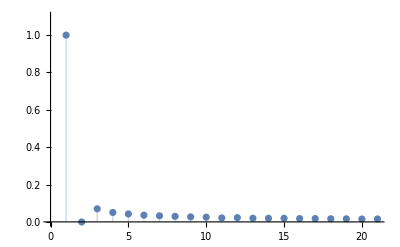

1.51571

```mathematica
cf=CorrelationFunction[l,{20}]
ListPlot[cf,Filling->0,PlotRange->{0,1.1}]
Total[cf]
```